```mathematica
f[x_]:=x^2-1
```

```mathematica
thing[xi_, w_, n_:20]:=Riffle[Transpose[{NestList[f, xi, n], NestList[f, w, n]}],Transpose[{NestList[f, w, n], NestList[f, f[xi], n]}]]
```

```mathematica
ComplexPointPlot[points_, range_:Automatic]:=ListPlot[Table[Style[{Re[p[[1]]], Im[p[[1]]]}, Hue[LogisticSigmoid[Im[p[[2]]]], 1,(1+LogisticSigmoid[Re[p[[2]]]])/2]], {p, points}], PlotRange->range]
```

```mathematica
error[points_]:=Sum[Abs[f[p[[1]]]-p[[2]]]^2, {p, points}]
errorFunc[xi_, w_]:=error[thing[xi, w]]
```

```mathematica
solo=NMinimize[errorFunc[xiRe+I xiIm, wRe + I wIm], {xiRe, xiIm, wRe, wIm}]
sol=Association@Last@solo;
xiS=sol[xiRe]+I sol[xiIm];
wS=sol[wRe] + I sol[wIm];
```

{1.52777,{xiRe→-0.618067,xiIm→-7.08325×10^-9,wRe→0.618003,wIm→-5.22421×10^-9}}

```mathematica
(points=thing[xiS, wS, 20])[[;;10]]//Grid
```

-0.618067-7.08325×10^-9 ⅈ | 0.618003-5.22421×10^-9 ⅈ
0.618003-5.22421×10^-9 ⅈ | -0.617993+8.75585×10^-9 ⅈ
-0.617993+8.75585×10^-9 ⅈ | -0.618073-6.45716×10^-9 ⅈ
-0.618073-6.45716×10^-9 ⅈ | -0.618084-1.08221×10^-8 ⅈ
-0.618084-1.08221×10^-8 ⅈ | -0.617986+7.98198×10^-9 ⅈ
-0.617986+7.98198×10^-9 ⅈ | -0.617972+1.3378×10^-8 ⅈ
-0.617972+1.3378×10^-8 ⅈ | -0.618093-9.86551×10^-9 ⅈ
-0.618093-9.86551×10^-9 ⅈ | -0.618111-1.65344×10^-8 ⅈ
-0.618111-1.65344×10^-8 ⅈ | -0.617961+1.21956×10^-8 ⅈ
-0.617961+1.21956×10^-8 ⅈ | -0.617939+2.04402×10^-8 ⅈ

```mathematica
pRange=AbsoluteOptions[ComplexPointPlot[points],PlotRange][[1,2]];
ListAnimate[Table[ComplexPointPlot[points[[;;n]], pRange], {n, Length[points]}]]
```

```mathematica
p2=(Re/@#)&/@points
```

{{-0.618067,0.618003},{0.618003,-0.617993},{-0.617993,-0.618073},{-0.618073,-0.618084},{-0.618084,-0.617986},{-0.617986,-0.617972},{-0.617972,-0.618093},{-0.618093,-0.618111},{-0.618111,-0.617961},{-0.617961,-0.617939},{-0.617939,-0.618125},{-0.618125,-0.618151},{-0.618151,-0.617922},{-0.617922,-0.617889},{-0.617889,-0.618172},{-0.618172,-0.618214},{-0.618214,-0.617863},{-0.617863,-0.617812},{-0.617812,-0.618245},{-0.618245,-0.618308},{-0.618308,-0.617773},{-0.617773,-0.617695},{-0.617695,-0.618357},{-0.618357,-0.618453},{-0.618453,-0.617635},{-0.617635,-0.617516},{-0.617516,-0.618527},{-0.618527,-0.618674},{-0.618674,-0.617424},{-0.617424,-0.617242},{-0.617242,-0.618788},{-0.618788,-0.619012},{-0.619012,-0.617102},{-0.617102,-0.616824},{-0.616824,-0.619186},{-0.619186,-0.619528},{-0.619528,-0.616609},{-0.616609,-0.616185},{-0.616185,-0.619793},{-0.619793,-0.620316},{-0.620316,-0.615857},{-0.615857,-0.615208}}

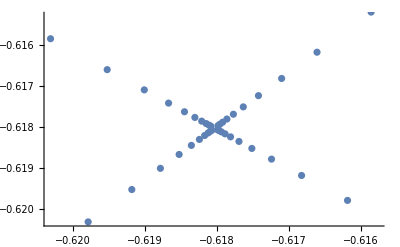

```mathematica
Show[ListPlot[p2], Plot[Cos[x], {x, -1, 1}]]
```

```mathematica
LinearSpline[points_][x_]:=Module[{p, m, xs,table},
p=Sort[points,#1[[1]]<#2[[1]]&];
m=If[#1==0,2^16,(#2/#1)]&@@@(Drop[p,1]-Drop[p, -1]);
table=Table[{Drop[p,-1][[i,1]]<=x<Drop[p, 1][[i,1]],m[[i]]*(x-Drop[p,1][[i,1]])+Drop[p,1][[i,2]]},{i,Length[p]-1}];
table=Flatten@Join[{x<p[[1,1]], table[[1,2]]}, table, {x>=p[[-1,1]], table[[-1,2]]}];
Which@@table
]
```

```mathematica
g=LinearSpline[p2];
```

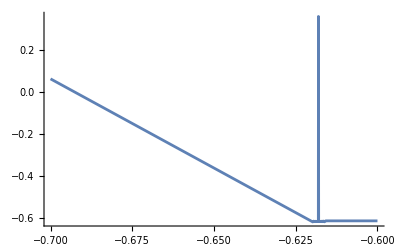

```mathematica
Plot[g[x], {x, -0.7, -0.6}]
```